```mathematica
SetDirectory["D:\\Users\\Matt\\OneDrive\\Documents\\Course Notes\\Calculus 1\\Figures"]; (* for home desktop *)
```

```mathematica
SetDirectory["C:\\Users\\matth\\OneDrive\\Mathematics\\calculus-notes\\Figures"]; (* for laptop *)
```

```mathematica
vp=Options[Graphics3D,ViewPoint][[1,2]];
```

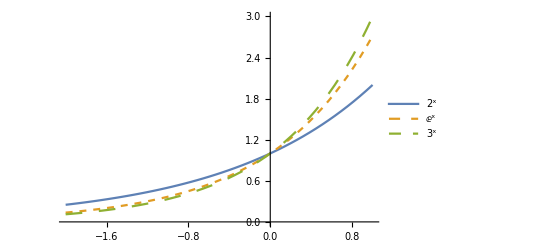

```mathematica
expfunctions
```

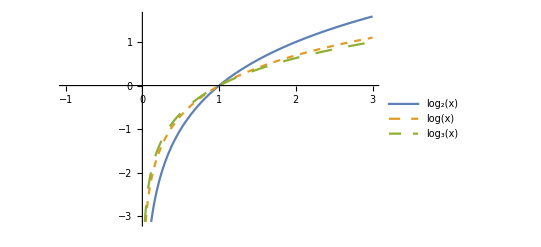

```mathematica
logfunctions = Plot[{Log[2, x], Log[x], Log[3,x]}, {x, -1, 3}, PlotStyle->{Automatic, Dashed, Dashing[0.03]}, PlotLegends->"Expressions"]
```

```mathematica
Export["logfunctions.pdf", logfunctions];
```

```mathematica
$InverseTrigFunctions={ArcSin,ArcCos,ArcSec,ArcCsc,ArcTan,ArcCot};
```

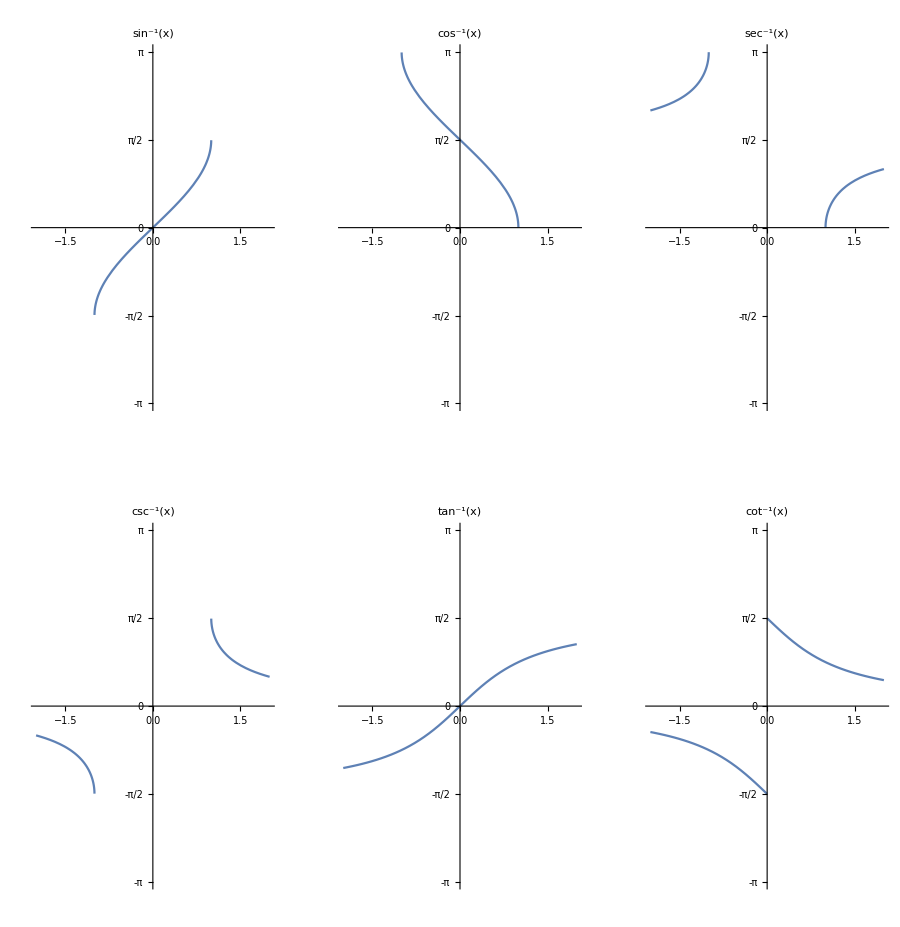

```mathematica
invtrigfunctions = GraphicsGrid[Partition[Table[Plot[f[x], {x, -2,2}, PlotRange->{{-2,2}, {-Pi, Pi}},AspectRatio->Pi/2,Ticks->{Automatic, Range[-1,1,1/2]*Pi},TicksStyle->12,PlotLabel->Style[f[x],18]], {f, $InverseTrigFunctions}],3], ImageSize->900]
```

```mathematica
Export["invtrigfunctions.pdf", invtrigfunctions];
```

```mathematica
{a,b}+0.1
```

{0.1+a,0.1+b}

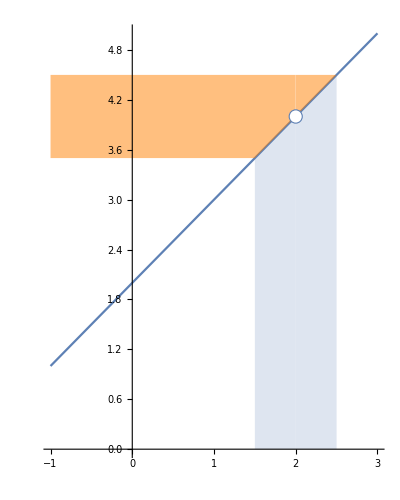

```mathematica
deflimitplot = Show[
Plot[(x^2-4)/(x-2), {x, -1, 3},PlotRange->{Automatic, {0,5}}, AspectRatio->5/4, Epilog->{EdgeForm[{Thick, ColorData[97][1]}],FaceForm[White], Disk[{2,4}, 0.08]}],
Plot[(x^2-4)/(x-2), {x, 1.5, 2.5},PlotRange->{Automatic, {0,5}}, AspectRatio->5/4, Filling->Axis, PlotStyle->Opacity[0]],
Plot[(x^2-4)/(x-2), {x, -1,3},PlotRange->{Automatic, {3.5, 4.5}}, AspectRatio->5/4, Filling->4.5, PlotStyle->Opacity[0], FillingStyle->Directive[Orange, Opacity[0.5]]]
]
```

```mathematica
Export["deflimitplot.pdf", deflimitplot];
```

```mathematica
Show[
Plot3D[x^y, {x, -1, 1}, {y, -1, 1}, AxesLabel->Automatic, AxesStyle->14, AxesOrigin->{0,0,0},Boxed->False,ClippingStyle->None, PlotPoints->100, PlotStyle->Opacity[0.75]],
ParametricPlot3D[{{0, t, 0},{t, 0, 1}}, {t, -1, 1}, PlotStyle->{Red, Blue}]
]
```

-Graphics3D-

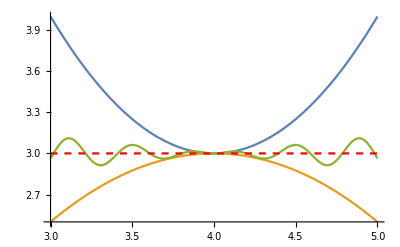

```mathematica
squeezethm = Show[
Plot[{(x-4)^2+3, -(x-4)^2/2 + 3, (x-4)Sin[16(x-4)]/8 + 3}, {x, 3, 5}],
Plot[3, {x, 3, 5}, PlotStyle->Directive[Red, Dashed]]
]
```

```mathematica
Export["squeezethm.pdf", squeezethm];
```

```mathematica
f[x_]:=Sin[2.5x]+x;
tansecline = Show[
Plot[f[x], {x, 0, 4}, PlotRange->{Automatic, {0, 5}}],
Graphics[{Red, PointSize[Large], Point[{3, f[3]}], InfiniteLine[{{3,f[3]}, {3.5, f[3]+0.5f'[3]}}], Darker[Green],Dashed, Point[{1, f[1]}], InfiniteLine[{{1, f[1]},{3, f[3]}}]}]
]
```